```mathematica
SetDirectory@NotebookDirectory[];
Import["path to QuESTlink.m"];
CreateLocalQuESTEnv["path to quest_link"];
(*Read the paper [Tyson Jones and Simon Benjamin, arXiv:1912.07904] for how to setup the environment.*)
```

## Parameters

```mathematica
numQb=2;
PI=N[π,12];
θ=7PI/16;
dϕ=2*PI/64;
Nϕ=64*10;
```

## QC

```mathematica
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Memristor Circuit

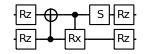

```mathematica
circMR={Subscript[Rz, 0][θ],Subscript[Rz, 1][θ],Subscript[C, 0][Subscript[X, 1]],Subscript[C, 1][Subscript[Rx, 0][PI-2θ]],Subscript[S, 1],Subscript[Rz, 1][-θ],Subscript[Rz, 0][-θ]};
DrawCircuit@circMR
```

## Initialisation Map

```mathematica
P0={{1,0},{0,0}};
SP={{0,1},{0,0}};
INI={P0,SP};
```

## Hysteresis Ry

```mathematica
HysteresisCC={};
HysteresisCM={};
InitZeroState[ρIN];
ApplyCircuit[{Subscript[H, 0]},ρIN,ρOUT];ρIN=ρOUT;
Do[(
ϕ=dϕ*(i-1);

circ={Subscript[Kraus, 1][INI],Subscript[Ry, 1][ϕ]};
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZIN=CalcExpecPauliSum[ρOUT,Subscript[Z, 1],ρWP];

circ=circMR;
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZOUT=CalcExpecPauliSum[ρOUT,Subscript[Z, 1],ρWP];
ZM=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];

AppendTo[HysteresisCC,{ZIN,ZOUT}];
AppendTo[HysteresisCM,{ZIN,ZM}];
),{i,Nϕ+1}];
```

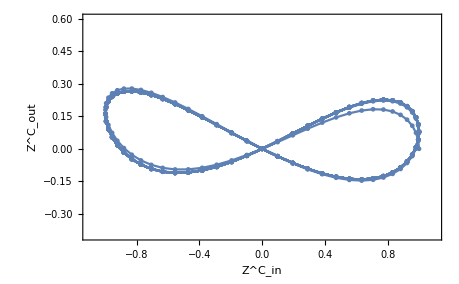

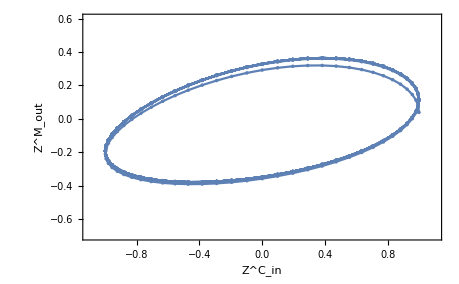

```mathematica
plotS=ListPlot[HysteresisCC,PlotRange->{{-1.1,1.1},{-0.4,0.6}},Axes->{False,False},Frame->True,FrameLabel->{"Z^C_in","Z^C_out"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotL=ListLinePlot[HysteresisCC];
plotCCRy=Show[plotS,plotL]
plotS=ListPlot[HysteresisCM,PlotRange->{{-1.1,1.1},{-0.7,0.6}},Axes->{False,False},Frame->True,FrameLabel->{"Z^C_in","Z^M_out"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotL=ListLinePlot[HysteresisCM];
plotCMRy=Show[plotS,plotL]
```

## Hysteresis Rx

```mathematica
HysteresisCC={};
HysteresisCM={};
InitZeroState[ρIN];
ApplyCircuit[{Subscript[H, 0]},ρIN,ρOUT];ρIN=ρOUT;
Do[(
ϕ=dϕ*(i-1);

circ={Subscript[Kraus, 1][INI],Subscript[Rx, 1][ϕ]};
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZIN=CalcExpecPauliSum[ρOUT,Subscript[Z, 1],ρWP];

circ=circMR;
ApplyCircuit[circ,ρIN,ρOUT];ρIN=ρOUT;
ZOUT=CalcExpecPauliSum[ρOUT,Subscript[Z, 1],ρWP];
ZM=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];

AppendTo[HysteresisCC,{ZIN,ZOUT}];
AppendTo[HysteresisCM,{ZIN,ZM}];
),{i,Nϕ+1}];
```

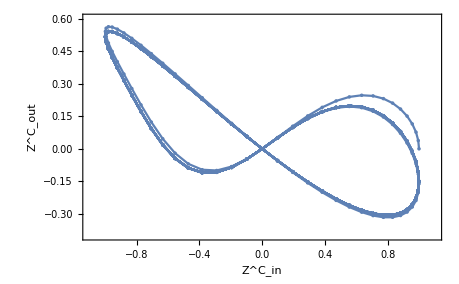

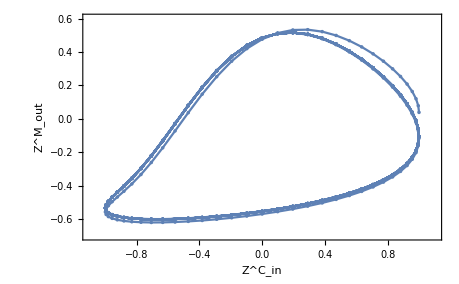

```mathematica
plotS=ListPlot[HysteresisCC,PlotRange->{{-1.1,1.1},{-0.4,0.6}},Axes->{False,False},Frame->True,FrameLabel->{"Z^C_in","Z^C_out"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotL=ListLinePlot[HysteresisCC];
plotCCRx=Show[plotS,plotL]
plotS=ListPlot[HysteresisCM,PlotRange->{{-1.1,1.1},{-0.7,0.6}},Axes->{False,False},Frame->True,FrameLabel->{"Z^C_in","Z^M_out"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotL=ListLinePlot[HysteresisCM];
plotCMRx=Show[plotS,plotL]
```